```mathematica
Lorenz方程数值求解
```

{{x→8.64099,y→8.64099,z→28.},{x→-8.64099,y→-8.64099,z→28.},{x→0.,y→0.,z→0.}}

{-13.9087,0.121028+10.3611 ⅈ,0.121028-10.3611 ⅈ}

{-13.9087,0.121028+10.3611 ⅈ,0.121028-10.3611 ⅈ}

{-23.1139,12.1139,-2.66667}

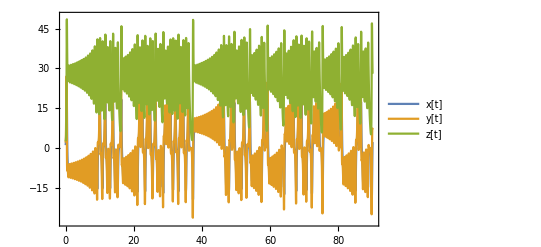

-Graphics3D-

```mathematica
Clear["Global`*"]
σ=10;(*系数，若改变该值，下面求本征值相关的代码需改动*)
γ=29;(*系数，该程序适合于γ>1时的情况*)
b=8/3;(*系数，若改变该值，下面求本征值相关的代码需改动*)
tt=90;(*时间*)

(*初始值*)
x0 = 1;
y0=2;
z0=3;

(*计算σ=10，b=8/3 时导数为0的点，对应的特征值*)
f = {0==σ*(y-x),0==γ*x-y-x*z,0==x*y-b*z};
sol = NSolve[f,{x,y,z}]
m={{-10,10,0},{1,-1,-Sqrt[8/3(γ-1)]},{Sqrt[8/3(γ-1)],Sqrt[8/3(γ-1)],-8/3}};
Eigenvalues[m]//N
m1={{-10,10,0},{1,-1,Sqrt[8/3(γ-1)]},{-Sqrt[8/3(γ-1)],-Sqrt[8/3(γ-1)],-8/3}};
Eigenvalues[m1]//N
m2={{-10,10,0},{γ,-1,0},{0,0,-8/3}};
Eigenvalues[m2]//N

(*数值求解洛伦兹方程*)
f = {D[x[t],t]==σ*(y[t]-x[t]),D[y[t],t]==γ*x[t]-y[t]-x[t]*z[t],D[z[t],t]==x[t]*y[t]-b*z[t],x[0]==x0,y[0]==y0,z[0]==z0};
s=NDSolve[f,{x,y,z},{t,0,tt},MaxSteps->Infinity];

(*为了确定作图范围而计算的一些数*)
N1 =tt/0.01;
x1 = Table[0,{N1+1}];
y1 = Table[0,{N1+1}];
z1 = Table[0,{N1+1}];
For[i=0,i≤N1,i=i+1,
t = i*0.01;
x1[[i+1]]=Evaluate[{x[t]}/.s][[1,1]];
y1[[i+1]]=Evaluate[{y[t]}/.s][[1,1]];
z1[[i+1]]=Evaluate[{z[t]}/.s][[1,1]];]
xmin = Min[x1]-1;
ymin = Min[y1]-1;
zmin = Min[z1]-1;
xmax = Max[x1]+1;
ymax = Max[y1]+1;
zmax = Max[z1]+1;
min = Min[xmin,ymin,zmin];
max = Max[xmax,ymax,zmax];

(*画x[t],y[t],z[t]图*)
p2 = ParametricPlot3D[{x[t],y[t],z[t]}/.s,{t,0,tt},PlotPoints->2000,Boxed->True,Axes->True,PlotRange->{{xmin,xmax},{ymin,ymax},{zmin,zmax}},PlotStyle->{Red,Thin}];

(*画洛伦兹方程数值求解的结果图*)
Plot[{Evaluate[{x[t],y[t],z[t]}/.s]},{t,0,tt},PlotLegends->{"x[t]","y[t]","z[t]"},PlotRange->{{0,tt},{min,max}},Frame->True]
Show[p2,Graphics3D[{{PointSize[0.02],Red,Point[{0,0,0}]},{PointSize[0.02],Red,Point[{x/.sol[[1]][[1]],y/.sol[[1]][[2]],z/.sol[[1]][[3]]}]},{PointSize[0.02],Red,Point[{x/.sol[[2]][[1]],y/.sol[[2]][[2]],z/.sol[[2]][[3]]}]},{PointSize[0.02],Blue,Point[{x0,y0,z0}]}
,Axes->True,Frame->True
}],PlotRange->{{xmin,xmax},{ymin,ymax},{zmin,zmax}},AxesLabel->{Style["x",15],Style["y",15],Style["z",15]},PlotLabel->"红点为导数为0的点，蓝点为起始点"]

(*画洛伦兹方程数值求解的结果动态图*)
Animate[Show[p2,Graphics3D[{{PointSize[0.02],Red,Point[{0,0,0}]},{PointSize[0.02],Red,Point[{x/.sol[[1]][[1]],y/.sol[[1]][[2]],z/.sol[[1]][[3]]}]},{PointSize[0.02],Red,Point[{x/.sol[[2]][[1]],y/.sol[[2]][[2]],z/.sol[[2]][[3]]}]},{PointSize[0.02],Blue,Point[{x0,y0,z0}]},
{PointSize[0.03],Blue,Point[{Evaluate[{x[t]}/.s][[1,1]],Evaluate[{y[t]}/.s][[1,1]],Evaluate[{z[t]}/.s][[1,1]]}]}
,Axes->True,Frame->True
}],PlotRange->{{xmin,xmax},{ymin,ymax},{zmin,zmax}},AxesLabel->{Style["x",15],Style["y",15],Style["z",15]}],{t,0,tt},AnimationRate->0.3]
```